```mathematica
SetDirectory[NotebookDirectory[]]
Get["Necessary Functions.m"]
```

I:\HarmonicDrums

{pluck, peak, parametricregion, egsystem, QOtriangleApprox, freqsintens, graphfi, keep, loudfreqs, graphweight, colorfreqs, freqband, freqlines, print3Dborder, print3Dregion, p, vard, disvector,soundanalysispg,comparetheovals}

## Parallelograms with changing ‘tilt’

```mathematica
parallelogramx[ϵ_][t_]:=p[{{0,0},{1,0},{1+ϵ,1},{ϵ,1},{0,0}}][t][[1]]; (* 0≤ϵ<2 *)
parallelogramy[ϵ_][t_]:=p[{{0,0},{1,0},{1+ϵ,1},{ϵ,1},{0,0}}][t][[2]]; (* 0≤t≤4 *)
parallelogramregion[ϵ_]:=parametricregion[{parallelogramx[ϵ],parallelogramy[ϵ]},{0,4}]
centerpara[ϵ_]:={(1+ϵ)/2,1/2};
paraeigentable[ϵ_]:=Module[{region,vals,funcs},
region=Evaluate[parallelogramregion[ϵ]];
{vals,funcs}=egsystem[region];
Table[Plot3D[funcs[[i]][x,y],{x,y}∈region],{i,1,Length[funcs]}]]
parafi[epsilon_]:=Module[{x,y,thumpoint,umin,umax,graphic},
x[ϵ_][t_]:=p[{{0,0},{1,0},{1+ϵ,1},{ϵ,1},{0,0}}][t][[1]];
y[ϵ_][t_]:=p[{{0,0},{1,0},{1+ϵ,1},{ϵ,1},{0,0}}][t][[2]];
thumpoint[ϵ_]:=centerpara[ϵ];
graphic[ϵ_]:={Show[ParametricPlot[{x[ϵ][u],y[ϵ][u]},{u,0,4},PlotLabel->ϵ],ListPlot[{thumpoint[ϵ]},PlotStyle->PointSize[0.02]]],
graphfi[{{x[ϵ],y[ϵ]},{0,4}},15][{thumpoint[ϵ]}]};
graphic[epsilon]];
```

### Overall Picture

```mathematica
ϵrange=Table[parafi[ϵ],{ϵ,0,0.8,0.1}];
GraphicsGrid[ϵrange,Frame->All]
```

-Graphics-

## Ellipses with changing major axis “L”

```mathematica
ellipsefi[axis_]:=Module[{x,y,thumpoint,umin,umax,graphic},
x[L_][t_]:=L Cos[t];
y[t_]:=Sin[t];
graphic[L_]:={Show[ParametricPlot[{x[L][u],y[u]},{u,0,2Pi}],ListPlot[{{0,0}},PlotStyle->PointSize[0.02]]],
graphfi[{{x[L],y},{0,2Pi}},15][{{0,0}}]};
graphic[axis]];
```

### Overall Picture

```mathematica
Lrange=Table[ellipsefi[L],{L,1,5,0.5}];
GraphicsGrid[Lrange,Frame->All]
```

-Graphics-

## Using NMinimize with Triangle

```mathematica
goodtriangle[{x_?NumericQ}]:=Module[{trix,triy,tripara,region,trisys,chosen},
Clear[trix,triy,tripara,region,trisys,chosen];
trix[t_]:=p[{{-2,-2},{x,1},{2,-2},{-2,-2}}][t][[1]];
triy[t_]:=p[{{-2,-2},{x,1},{2,-2},{-2,-2}}][t][[2]];
tripara={{trix,triy},{0,3}};
region=parametricregion[tripara];
trisys=egsystem[20][region];
If[Length[trisys]!=2,
100,
chosen=trisys[[1,#]]&/@loudfreqs[trisys[[2]],0.15];
(chosen[[2]]/chosen[[1]]-2)^2]]
```

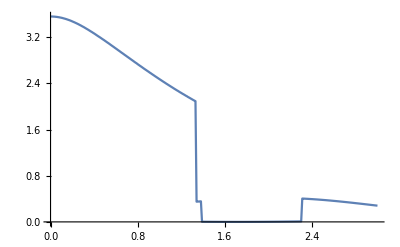

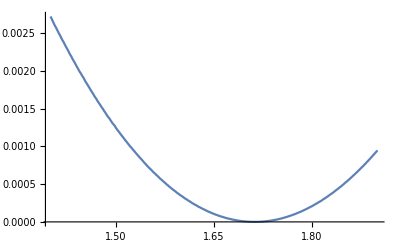

```mathematica
Module[{xvals,vals,inter,xgenvals,valsgen},
xgenvals=Table[{x},{x,0,3,1/100}];
xvals=Table[{x},{x,1.4,1.9,0.5/300}];
valsgen=goodtriangle/@xgenvals;
vals=goodtriangle/@xvals;
Print[ListLinePlot[Table[{xgenvals[[i]][[1]],valsgen[[i]]},{i,Length[vals]}]]];
Print[ListLinePlot[Table[{xvals[[i]][[1]],vals[[i]]},{i,Length[vals]}]]];];//Quiet
```

```mathematica
goodtriangle[1.7]
```

3.96268×10^-6

```mathematica
NMinimize
```

## Bulge on Circle

```mathematica
bulgycircle[a_?Positive]:=Module[{pts,fst,ptsrepeat,ordered},
pts={{1,0},{0,-1},{-1,0},{0,1},{a,a}};
ptsrepeat=Join[pts,pts[[2;;5]]];
{{Interpolation[ptsrepeat[[All,1]],Method->"Spline"],Interpolation[ptsrepeat[[All,2]],Method->"Spline"]},{3,Length[ptsrepeat]-2}}];
measure[a_?Positive]:=Module[{paramet,region,esys,weights,displacement},
paramet=bulgycircle[a];
region=parametricregion[paramet];
esys=egsystem[15][region];
weights=QOtriangleApprox[esys[[2]]];
displacement=disvector[][esys[[1]]];
Norm[Table[weights[[i]]*displacement[[i]],{i,Length[displacement]}]]];
```

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix SparseArray[Automatic,«2»,{1,{{0,«8019»,82398},{«1»}},{5.35639×10^-7,-1.33385×10^-8,-3.47011×10^-8,-4.38666×10^-8,-5.56907×10^-8,-1.18262×10^-7,2.15613×10^-20,-9.74419×10^-21,-3.43034×10^-8,«82380»,2.84603×10^-19,-0.000152313,-0.000286751,1.49078×10^-19,0.00060925,0.001147,0.001147,0.00060925,0.00351251}}] in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

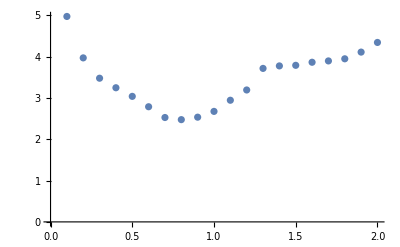

```mathematica
Module[{test,vals},
test=Range[0.1,2,0.1];
vals=measure[#]&/@test;
ListPlot[Table[{test[[i]],vals[[i]]},{i,Length[vals]}]]]
```

```mathematica
NMinimize[measure[a],{a}∈Interval[{10^-10,2.5}],MaxIterations->10,Method->"DifferentialEvolution"]
```

{2.46847,{a→0.779624}}

## Interpolation of 4 Points

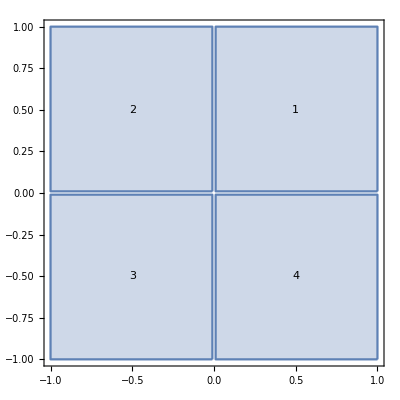

```mathematica
para4pts[{{x1_?NumericQ,y1_?NumericQ},{x2_?NumericQ,y2_?NumericQ},{x3_?NumericQ,y3_?NumericQ},{x4_?NumericQ,y4_?NumericQ}}]:=Module[{pts,fst,ordered,ptsrepeat},
pts={{x1,y1},{x2,y2},{x3,y3},{x4,y4}};
fst=FindShortestTour[pts];
ordered=pts[[fst[[2]]]];
ptsrepeat=Join[ordered,ordered[[2;;5]]];
{{Interpolation[ptsrepeat[[All,1]],Method->"Spline"],Interpolation[ptsrepeat[[All,2]],Method->"Spline"]},{3,Length[ptsrepeat]-2}}];
good4pts[{{x1_?NumericQ,y1_?NumericQ},{x2_?NumericQ,y2_?NumericQ},{x3_?NumericQ,y3_?NumericQ},{x4_?NumericQ,y4_?NumericQ}}]:=Module[{paramet,esys,weights,displacement},
paramet=para4pts[{{x1,y1},{x2,y2},{x3,y3},{x4,y4}}];
esys=egsystem[20][parametricregion[paramet]];
weights=QOtriangleApprox[esys[[2]]];
displacement=disvector[1][esys[[1]]];
Norm[Table[weights[[i]]*displacement[[i]],{i,Length[displacement]}]]];
fouregions[ϵ_:0.1]:={Rectangle[{ϵ,ϵ},{1,1}],Rectangle[{-1,ϵ},{-ϵ,1}],Rectangle[{-1,-1},{-ϵ,-ϵ}],Rectangle[{ϵ,-1},{1,-ϵ}]};
RegionPlot[fouregions[10^-2],Epilog->{Text[1,{0.5,0.5}],Text[2,{-0.5,0.5}],Text[3,{-0.5,-0.5}],Text[4,{0.5,-0.5}]}]
```

```mathematica
freg=fouregions[10^-2];
posol=NMinimize[{good4pts[{{x1,y1},{x2,y2},{x3,y3},{x4,y4}}],{x1,y1}∈freg[[1]],{x2,y2}∈freg[[2]],{x3,y3}∈freg[[3]],{x4,y4}∈freg[[4]]},{x1,y1,x2,y2,x3,y3,x4,y4},Method->"DifferentialEvolution",MaxIterations->5]
```

NMinimize::nnum: The function value Abs[BoundaryMeshRegion[{{-0.742524,-0.846516},{-0.742742,-0.845423},{-0.742955,-0.844322},{-0.743366,-0.842096},{-0.743564,-0.84097},{-0.743757,-0.839837},«40»,{-0.74726,-0.774857},{-0.747214,-0.773347},{-0.747163,-0.77183},{-0.747108,-0.770306},«704»},Line[{«1»}]] «1»⟦2⟧] is not a number at {x1,x2,x3,x4,y1,y2,y3,y4} = {0.421392,-0.0225747,-0.742524,0.376284,0.134623,0.878337,-0.846516,-0.032731}.

{2.9995,{x1→0.749666,x2→-0.554532,x3→-0.7636,x4→0.377762,y1→0.721523,y2→0.706354,y3→-0.174429,y4→-0.819565}}

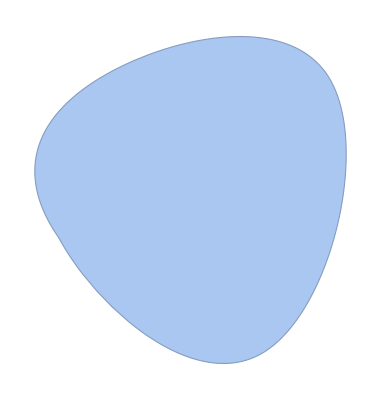

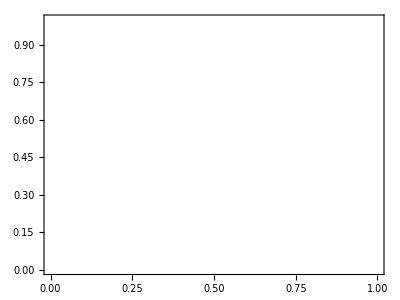

```mathematica
Module[{para,region,sys},
para=para4pts[{{x1,y1},{x2,y2},{x3,y3},{x4,y4}}/.posol[[2]]];
Print[region=parametricregion[para]];
sys=egsystem[20][region];
Graphics[Table[InfiniteLine[{freq,0},{0,1}],{freq,sys[[1]]}],Frame->True]]
```

## Interpolation of 5 Points

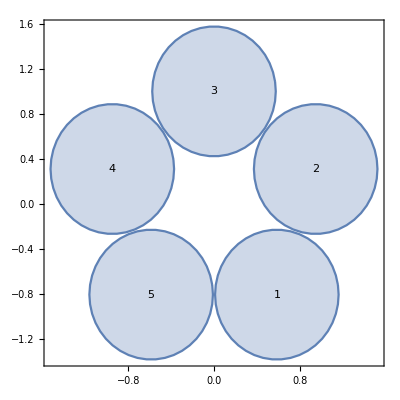

```mathematica
para5pts[{{x1_?NumericQ,y1_?NumericQ},{x2_?NumericQ,y2_?NumericQ},{x3_?NumericQ,y3_?NumericQ},{x4_?NumericQ,y4_?NumericQ},{x5_?NumericQ,y5_?NumericQ}}]:=Module[{pts,fst,ordered,ptsrepeat},
pts={{x1,y1},{x2,y2},{x3,y3},{x4,y4},{x5,y5}};
fst=FindShortestTour[pts];
ordered=pts[[fst[[2]]]];
ptsrepeat=Join[ordered,ordered[[2;;5]]];
{{Interpolation[ptsrepeat[[All,1]],Method->"Spline"],Interpolation[ptsrepeat[[All,2]],Method->"Spline"]},{3,Length[ptsrepeat]-2}}];
good5pts[{{x1_?NumericQ,y1_?NumericQ},{x2_?NumericQ,y2_?NumericQ},{x3_?NumericQ,y3_?NumericQ},{x4_?NumericQ,y4_?NumericQ},{x5_?NumericQ,y5_?NumericQ}}]:=Module[{paramet,esys,weights,displacement},
paramet=para5pts[{{x1,y1},{x2,y2},{x3,y3},{x4,y4},{x5,y5}}];
esys=egsystem[20][parametricregion[paramet]];
weights=QOtriangleApprox[esys[[2]]];
displacement=disvector[1][esys[[1]]];
Norm[Table[weights[[i]]*displacement[[i]],{i,Length[displacement]}]]];
circleregions[Num_,ϵ_:0.1]:=Module[{centers,radius},
centers=CirclePoints[Num];
radius=0.5 √((centers[[1,1]]-centers[[2,1]])^2+(centers[[1,2]]-centers[[2,2]])^2)-ϵ;
Table[Disk[centers[[i]],radius],{i,Num}]]
RegionPlot[circleregions[5,0.01],Epilog->Table[Text[i,CirclePoints[5][[i]]],{i,5}]]
```

```mathematica
fiveregions=circleregions[5,0.01];
centers=CirclePoints[5];
limits=Table[{centers[[i,j]]-0.1,centers[[i,j]]+0.1},{i,5},{j,2}];
posol5=NMinimize[{good5pts[{{x1,y1},{x2,y2},{x3,y3},{x4,y4},{x5,y5}}],
{x1,y1}∈fiveregions[[1]],{x2,y2}∈fiveregions[[2]],{x3,y3}∈fiveregions[[3]],{x4,y4}∈fiveregions[[4]],{x5,y5}∈fiveregions[[5]]},
{{x1,limits[[1,1,1]],limits[[1,1,2]]},{y1,limits[[1,2,1]],limits[[1,2,2]]},{x2,limits[[2,1,1]],limits[[2,1,2]]},{y2,limits[[2,2,1]],limits[[2,2,2]]},{x3,limits[[3,1,1]],limits[[3,1,2]]},{y3,limits[[3,2,1]],limits[[3,2,2]]},{x4,limits[[4,1,1]],limits[[4,1,2]]},{y4,limits[[4,2,1]],limits[[4,2,2]]},{x5,limits[[5,1,1]],limits[[5,1,2]]},{y5,limits[[5,2,1]],limits[[5,2,2]]}},
Method->"DifferentialEvolution",MaxIterations->5]
```

{{{0.487785,0.687785},{-0.909017,-0.709017}},{{0.851057,1.05106},{0.209017,0.409017}},{{-0.1,0.1},{0.9,1.1}},{{-1.05106,-0.851057},{0.209017,0.409017}},{{-0.687785,-0.487785},{-0.909017,-0.709017}}}

$Aborted

## Interpolation of n Points

```mathematica
parapts[ptslist_?(MatrixQ[#,NumericQ]&)]:=Module[{fst,ordered,pts,int},
fst=FindShortestTour[ptslist];
ordered=ptslist[[fst[[2]]]];
pts=Join[ordered,ordered[[2;;-1]],ordered[[2;;-1]]];
{Table[Interpolation[pts[[All,i]],Method->"Spline"],{i,2}],{Length[ptslist],2Length[ptslist]}}];

paraplot[{{f_,g_},{umin_,umax_}}]:=ParametricPlot[{f[u],g[u]},{u,umin,umax},PlotRange->All];

goodpts::nonMR="Input `1` does not form a BoundaryMeshRegion.";
frames={};
goodpts[ptslist_?(MatrixQ[#,NumericQ]&)]:=Module[{paramet,region,sys,weights,displacement},
paramet=parapts[ptslist];
region=parametricregion[paramet];
If[BoundaryMeshRegionQ[region],
(AppendTo[frames,RegionPlot[region,PlotRange->{{-1,1},{-1,1}}]];
sys=egsystem[20][region];
weights=QOtriangleApprox[sys[[2]]];
displacement=disvector[1][sys[[1]]];
Norm[Table[weights[[i]]*displacement[[i]],{i,Length[displacement]}]]),
(Message[goodpts::nonMR,ptslist];
Print[paraplot[paramet]];
100)]];
```

```mathematica
Module[{points,box},
Off[General::stop,BoundaryMeshRegion::binsect];
points={p1,p2,p3,p4};
box=Rectangle[{-1,-1},{1,1}];
{posol,evals}=Reap[NMinimize[goodpts[points],Table[p∈box,{p,points}],MaxIterations->5,Method->"DifferentialEvolution",
EvaluationMonitor->Sow[points,"VisitedPoint"]],"VisitedPoint"];
On[General::stop,BoundaryMeshRegion::binsect];
Print[posol];]
```

$Aborted

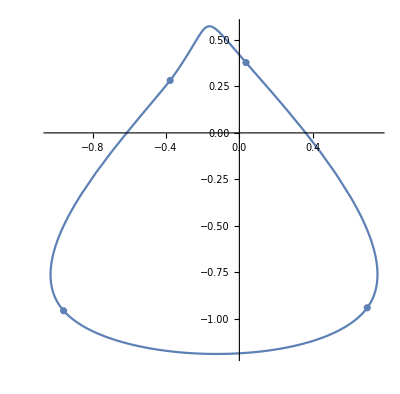

```mathematica
Module[{pts,para,pplot},
pts={p1,p2,p3,p4}/.posol[[2]];
para=parapts[pts];
pplot=ParametricPlot[{para[[1,1]][u],para[[1,2]][u]},{u,para[[2,1]],para[[2,2]]}];
Print[Show[pplot,ListPlot[pts]]];]
```

## NMaximize and Polygons

Needs to use NMaximize instead of NMinimize, and will use Polygons instead of simple closed curves.

```mathematica
RepeatedTiming[Module[{reg,points,fst},
points=RandomPoint[Disk[],5];
fst=FindShortestTour[points];
reg=Polygon[points[[fst[[2]]]]];
Sqrt[NDEigenvalues[{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},{u},{x,y}∈reg,5]]],5]
```

{0.071,{9.64102,12.5023,14.6527,15.9492,17.4712}}

### Using Ratio of First two frequencies

```mathematica
goodPolygon2F[pointslist_?(MatrixQ[#,NumericQ]&)]:=Module[{fst,reg,freqs},
fst=FindShortestTour[pointslist];
reg=Polygon[pointslist[[fst[[2]]]]];
freqs=Sqrt[NDEigenvalues[{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},{u},{x,y}∈reg,2]];
1/(freqs[[2]]/freqs[[1]]-2)^2];
```

```mathematica
Module[{points,box},
points={x1,y1,x2,y2,x3,y3,x4,y4};
box=Rectangle[{-1,-1},{1,1}];
vals2F={};
posol2F=NMaximize[Prepend[Table[-1≤p≤1,{p,points}],goodPolygon2F[Partition[points,2]]],points,
MaxIterations->3,Method->"DifferentialEvolution",
EvaluationMonitor:>AppendTo[vals2F,Evaluate[goodPolygon2F[Partition[points,2]]]]];
Print[posol2F];]//AbsoluteTiming
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 3 iterations.

{4.67877,{x1→0.924621,y1→0.735913,x2→-0.182384,y2→-0.331903,x3→0.0746796,y3→0.917356,x4→1.,y4→-0.194145}}

{137.299,Null}

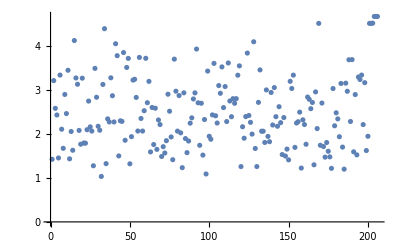

```mathematica
ListPlot[vals2F]
```

```mathematica
Length[vals2F]
```

206

```mathematica
vals2F[[-50;;-1]]
```

{2.49986,1.22566,2.32437,2.21731,1.76776,2.84333,2.79204,2.57871,2.7196,1.30017,2.96101,2.125,4.52109,1.74564,2.70617,1.71612,1.4748,1.80727,1.6086,1.48084,1.21937,3.0371,2.18822,2.48438,2.34647,1.93976,3.15263,1.70341,1.20092,3.15919,2.97476,3.6922,2.28693,3.69634,1.59573,2.89985,1.52673,3.2996,3.24227,3.34402,2.21657,3.17095,1.62481,1.94992,4.52109,4.52109,4.52655,4.67872,4.67877,4.67877}

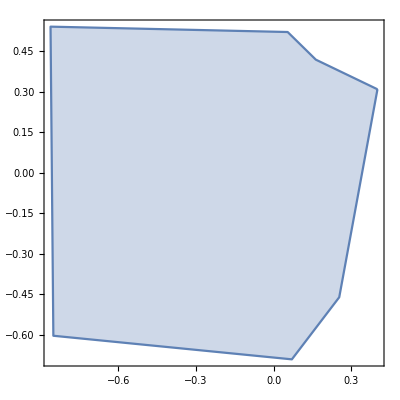

{1.,1.58366,1.58482,2.03003,2.21385}

-Graphics-

```mathematica
Module[{fst,pts,reg,freqs},
pts={{x1,y1},{x2,y2},{x3,y3},{x4,y4},{x5,y5},{x6,y6},{x7,y7}}/.posol2F[[2]];
fst=FindShortestTour[pts];
reg=Polygon[pts[[fst[[2]]]]];
Print[RegionPlot[reg]];
freqs=Sqrt[NDEigenvalues[{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},{u},{x,y}∈reg,5]];
Print[freqs/freqs[[1]]];
Play[Total[Sin[440 # t 2 π]&/@(freqs/freqs[[1]])],{t,0,2}]]
```

#### Bad Points

{{-0.181724,0.315404},{0.57919,-0.349315},{-0.505478,0.294577},{-0.383731,0.959505},{0.855043,-0.957356}}

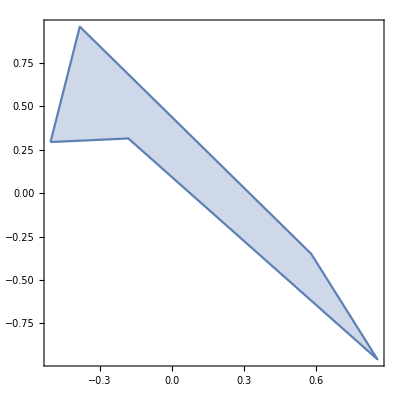

```mathematica
Module[{fst},
badpts={p1,p2,p3,p4,p5}/.posol[[2]];
fst=FindShortestTour[pts];
Print[badpts];
RegionPlot[Polygon[badpts[[fst[[2]]]]]]]
```

### Using Nueral Network

```mathematica
(* frequencies need to be normalized so that the all are divided by the fundamental, takes 5 frequencies in a list *)
predict=Module[{full,start,nogood,fixed,ts,normalize,nts,ntsimperfect,newt,fixednewt},
full=Import["http://physics.hamline.edu/~arundquist/drums/sound/mathematica","TSV"];
start=DateObject["2016-07-26 13:30:00"];
nogood={572,1167,1361,1377};
fixed=Select[full,(!MemberQ[nogood,#[[1]]])&&QuantityMagnitude[DateDifference[start,DateObject[#[[-1]]]]]>0&];
ts=Sort[ToExpression[#[[2]]]]->#[[4]]&/@fixed;
normalize[candidate_]:=(f1=1.0candidate[[1,1]];
candidate[[1]]/f1->candidate[[2]]);
nts=Table[{f=RandomReal[{-100,150}],2f,3f,4f,5f}->6,{100}];
ntsimperfect=Table[{f=RandomReal[{-100,150}],2f+RandomReal[{-5,5}],3f+RandomReal[{-5,5}],4f+RandomReal[{-5,5}],5f+RandomReal[{-5,5}]}->5.5,{100}];
newt=Join[nts,ts,ntsimperfect];
fixednewt=normalize/@newt;
Predict[fixednewt,Method->"NeuralNetwork"]];

goodPolygonNN[ptslist_?(MatrixQ[#,NumericQ]&)]:=Module[{fst,reg,freqs,normalized},
fst=FindShortestTour[ptslist];
reg=Polygon[ptslist[[fst[[2]]]]];
freqs=Sqrt[NDEigenvalues[{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},{u},{x,y}∈reg,5]];
normalized=freqs/freqs[[1]];
currentval=predict[normalized]];
```

#### RandomSearch

```mathematica
Module[{points},
ClearAll[evalsRS,posolRS];
points={x1,y1,x2,y2,x3,y3,x4,y4,x5,y5,x6,y6,x7,y7};
evalsRS={};
posolRS=Table[NMaximize[goodPolygonNN[Partition[points,2]],Table[{p,-1,1},{p,points}],
MaxIterations->10,Method->{"RandomSearch","SearchPoints"->210,"RandomSeed"->i},
EvaluationMonitor:>AppendTo[evalsRS,currentval]],{i,RandomInteger[{0,100},5]}]]
```

{{3.09708,{x1→0.0866816,y1→-0.392645,x2→0.218913,y2→-0.587995,x3→-0.247071,y3→0.848692,x4→0.219916,y4→0.0721744,x5→0.260705,y5→0.57119,x6→-0.695874,y6→0.156393,x7→0.665984,y7→0.212499}},{3.10265,{x1→0.911197,y1→0.669945,x2→0.114302,y2→-0.0997569,x3→-0.0317637,y3→0.0845266,x4→0.870749,y4→-0.415721,x5→0.42308,y5→0.994552,x6→0.495615,y6→0.502333,x7→0.757316,y7→0.446822}},{3.10976,{x1→-0.0671679,y1→-0.00077079,x2→-0.352742,y2→-0.527476,x3→-0.311733,y3→0.138003,x4→-0.016613,y4→0.0930654,x5→-0.785823,y5→-0.170222,x6→0.645715,y6→0.582993,x7→-0.650631,y7→0.971919}},{3.09324,{x1→0.00951345,y1→0.683682,x2→0.818571,y2→-0.392074,x3→0.363012,y3→-0.366444,x4→0.978598,y4→0.452374,x5→0.665304,y5→-0.0857996,x6→-0.417362,y6→-0.137772,x7→-0.0224515,y7→0.813483}},{3.09585,{x1→-0.530631,y1→0.0745578,x2→0.150106,y2→0.584221,x3→-0.326432,y3→0.808678,x4→-0.813779,y4→0.0225442,x5→-0.235857,y5→-0.0947262,x6→-0.584911,y6→0.497611,x7→-0.262755,y7→0.538893}}}

```mathematica
Speak["Done with Random Search"]
```

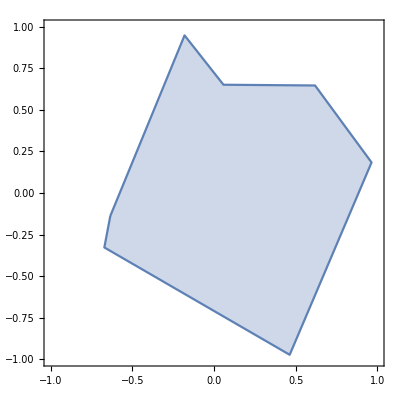

```mathematica
Module[{n,pts,fst,reg},
n=3;
pts={{x1,y1},{x2,y2},{x3,y3},{x4,y4},{x5,y5},{x6,y6},{x7,y7}}/.posolRS[[n,2]];
fst=FindShortestTour[pts];
reg=Polygon[pts[[fst[[2]]]]];
RegionPlot[reg,PlotRange->{{-1,1},{-1,1}},PlotLabel->posolRS[[n,1]]]]
```

```mathematica
Export["/Users/tomeichlersmith/Desktop/Summer Research 2016/Possible Solutions/RandomSearch 210S 5I.m",posolRS[[3]]]
```

/Users/tomeichlersmith/Desktop/Summer Research 2016/Possible Solutions/RandomSearch 210S 5I.m

```mathematica
bestRand=Import["/Users/tomeichlersmith/Desktop/Summer Research 2016/Possible Solutions/RandomSearch 210S 5I.m"]
```

{3.22706,{x1→-0.180082,y1→0.9475,x2→-0.670842,y2→-0.327353,x3→0.61828,y3→0.646298,x4→-0.634307,y4→-0.137929,x5→0.963824,y5→0.183636,x6→0.462954,y6→-0.972544,x7→0.0578378,y7→0.65081}}

```mathematica
Import["/Users/tomeichlersmith/Desktop/Summer Research 2016/Possible Solutions/PoSol 500G 50P.m"]
```

{3.2187,{x1→0.901424,x2→-0.250955,x3→-0.404856,x4→-0.338602,x5→0.406009,x6→-0.35846,x7→-0.734782,y1→-0.648723,y2→0.931306,y3→0.937017,y4→0.360545,y5→-0.684704,y6→0.919225,y7→0.457987}}

#### DifferentialEvolution

```mathematica
evalsDE={};
Module[{previousvals,points,initialpoints,min,pts},
previousvals={3.182999977187328,3.1852960338107117,3.188688386920378,0,0,0,0,0,0,0};
points={x1,y1,x2,y2,x3,y3,x4,y4,x5,y5,x6,y6,x7,y7};
initialpoints=Join[{points/.{x1->0.9169215799562568,y1->-0.522483035226656,x2->-0.8792121027248669,y2->-0.5553217080561086,x3->0.35260419867677883,y3->-0.741136219586096,x4->-0.34584595128823503,y4->-0.8705156275783515,x5->0.09085081416821189,y5->-0.14127069045593704,x6->0.008559482710790106,y6->-0.010476296699982679,x7->-0.09183333443024075,y7->-0.5480588676472485},
points/.{x1->0.9200958734705801,y1->-0.5122515943205607,x2->-0.8735773120074107,y2->-0.5524453172216844,x3->0.35375972688471097,y3->-0.7629823478170571,x4->-0.3451289906432142,y4->-0.8752481392367781,x5->0.08556480588685035,y5->-0.13324218363816653,x6->0.012588430921744356,y6->-0.024563341788597905,x7->-0.10125781329707853,y7->-0.528529555375023},
points/.{x1->0.9161835782743932,y1->-0.4936611196239482,x2->-0.8627695993721193,y2->-0.5230935468228799,x3->0.3653465538096488,y3->-0.8027169869773683,x4->-0.32683188309893585,y4->-0.8848817006607758,x5->0.061565772503552704,y5->-0.13392789522664966,x6->0.012802767936350412,y6->-0.01772317718570724,x7->-0.11425140701144071,y7->-0.5332572944539193}},
Table[RandomReal[{-1,1},14],{7}]];
Do[
posolDE=NMaximize[Prepend[Table[-1≤p≤1,{p,points}],goodPolygonNN[Partition[points,2]]],points,
MaxIterations->20,Method->{"DifferentialEvolution","SearchPoints"->10,"ScalingFactor"->0.3,"InitialPoints"->initialpoints,"CrossProbability"->0.75},EvaluationMonitor:>AppendTo[evalsDE,currentval]];
Print[posolDE];
min=Ordering[previousvals,1][[1]];
If[posolDE[[1]]>previousvals[[min]],
previousvals=ReplacePart[previousvals,min->posolDE[[1]]];
pts=points/.posolDE[[2]];
initialpoints=ReplacePart[initialpoints,min->pts];,
False];,
{10}];
Print[posolDE];
Print[previousvals];
Print[initialpoints];]
Speak["Done with Evolution"]
```

{3.15953,{x1→-0.206137,y1→0.816573,x2→-0.848632,y2→-0.992729,x3→-0.407941,y3→-0.931286,x4→-0.115226,y4→-0.24886,x5→-0.526707,y5→0.286595,x6→-0.202502,y6→0.220785,x7→-0.806003,y7→0.902882}}

{3.15953,{x1→-0.206137,y1→0.816573,x2→-0.848632,y2→-0.992729,x3→-0.407941,y3→-0.931286,x4→-0.115226,y4→-0.24886,x5→-0.526707,y5→0.286595,x6→-0.202502,y6→0.220785,x7→-0.806003,y7→0.902882}}

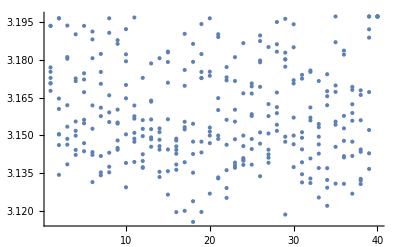

```mathematica
ListPlot[Table[{Ceiling[i/10],evalsDE[[i]]},{i,Length[evalsDE]}],PlotRange->All]
```

```mathematica
Export["/Users/tomeichlersmith/Desktop/Summer Research 2016/Possible Solutions/PossibleSol 50G 10P.m",posolDE]
```

/Users/tomeichlersmith/Desktop/Summer Research 2016/Possible Solutions/PossibleSol 50G 10P.m

```mathematica
circlemeas=predict[Sqrt[NDEigenvalues[{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},{u},{x,y}∈Disk[],5]]]
```

2.72088

#### NelderMead

```mathematica
Module[{points},
ClearAll[evalsNM,posolNM];
points={x1,y1,x2,y2,x3,y3,x4,y4,x5,y5,x6,y6,x7,y7};
evalsNM={};
posolNM=Do[NMaximize[goodPolygonNN[Partition[points,2]],Table[{p,-1,1},{p,points}],
MaxIterations->10,Method->{"NelderMead","RandomSeed"->i},
EvaluationMonitor:>AppendTo[evalsNM,currentval]],{i,RandomInteger[{0,100},5]}]]
Speak["Done with Nelder Mead"]
```

NMaximize::nnum: The function value -goodPolygonNN[{{-0.829939,0.78106},{0.35907,-0.375804},{-0.546506,0.555377},{0.293491,0.611624},{0.432956,0.358874},{-0.61609,-0.441663},{-0.208292,0.173329}}] is not a number at {x1,x2,x3,x4,x5,x6,x7,y1,y2,y3,y4,y5,y6,y7} = {-0.829939,0.35907,-0.546506,0.293491,0.432956,-0.61609,-0.208292,0.78106,-0.375804,0.555377,0.611624,0.358874,-0.441663,0.173329}.

General::stop: Further output of NMaximize::nnum will be suppressed during this calculation.

### 10 Gens, 30 Pop

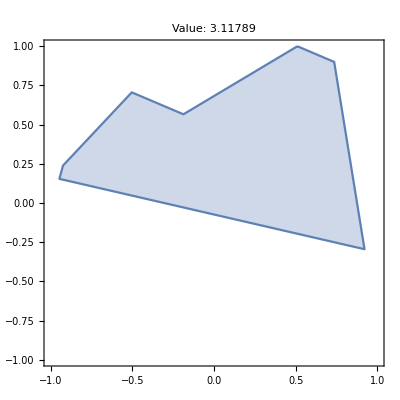

{4.33752,5.97453,6.98187,7.32232,8.96758}

{1.,1.37741,1.60964,1.68813,2.06744}

-Graphics-

```mathematica
Module[{posol,fst,points,reg,freqs},
posol=Import["/Users/tomeichlersmith/Desktop/Summer Research 2016/PossibleSol 10G 30P.m"];
points={{x1,y1},{x2,y2},{x3,y3},{x4,y4},{x5,y5},{x6,y6},{x7,y7}}/.posol[[2]];
fst=FindShortestTour[points];
reg=Polygon[points[[fst[[2]]]]];
Print[RegionPlot[reg,PlotRange->{{-1,1},{-1,1}},PlotLabel->"Value: "<>ToString[posol[[1]]]]];
freqs=Sqrt[NDEigenvalues[{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},{u},{x,y}∈reg,5]];
Print[freqs];
Print[(freqs/freqs[[1]])];
Play[Total[Sin[440 # t 2 Pi]&/@(freqs/freqs[[1]])],{t,0,2}]]
```

### Slicings of 10D Space (5 Control Points)

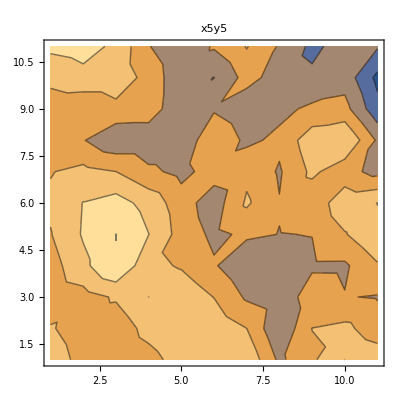

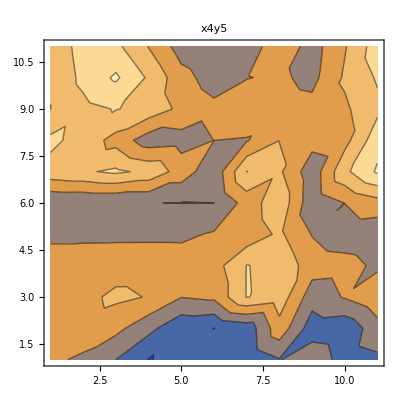

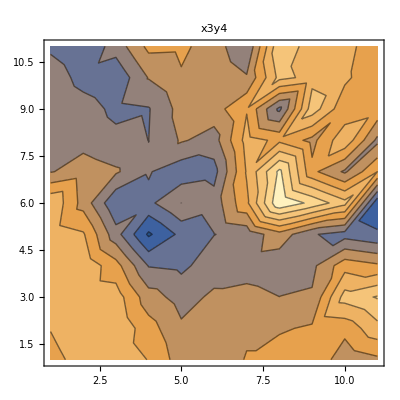

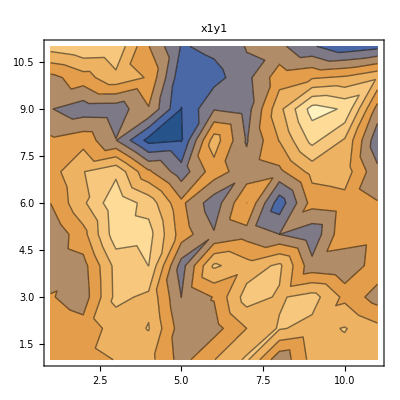

```mathematica
Module[{pts},
pts=RandomPoint[Rectangle[{-1,-1},{1,1}],5];
x5y5=Table[goodPolygonNN[Append[pts[[1;;4]],{x5,y5}]],
{x5,-1,1,1/5},{y5,-1,1,1/5}];
x4y5=Table[goodPolygonNN[Join[pts[[1;;3]],{{x4,pts[[4,2]]},{pts[[5,1]],y5}}]],
{x4,-1,1,1/5},{y5,-1,1,1/5}];
x3y4=Table[goodPolygonNN[Join[pts[[{1,2,5}]],{{x3,pts[[3,2]]},{pts[[4,1]],y4}}]],
{x3,-1,1,1/5},{y4,-1,1,1/5}];
x1y1=Table[goodPolygonNN[Prepend[pts[[2;;5]],{x1,y1}]],
{x1,-1,1,1/5},{y1,-1,1,1/5}];
Print[ListContourPlot[x5y5,PlotLabel->"x5y5"]];
Print[ListContourPlot[x4y5,PlotLabel->"x4y5"]];
Print[ListContourPlot[x3y4,PlotLabel->"x3y4"]];
Print[ListContourPlot[x1y1,PlotLabel->"x1y1"]];]
```